### Rozwiązanie stacjonarnego równania Schrödingera dla cząstki znajdującej się w studni potencjału przy warunku brzegowym ψ[ 0 ] = 0. Symbole "ψ[ x ]", "m", "E_n", "ℏ" oznaczają odpowiednio funkcję falową zależną od współrzędnej przestrzennej "x", masę cząstki i jej całkowitą energię oraz stałą Planka podzieloną przez liczbę 2 π.

```mathematica
ClearAll["Global`*"];
```

```mathematica
A=DSolve[{ℏ^2/(2×m)×D[ψ[x], x,x]==-En×ψ[x],ψ[0]==0},ψ[x],x];ψ1[x_]=ψ[x]/.A[[1,1]]
```

C[2] Sin[(√2 √En √m x)/ℏ]

### Wyodrębnienie argumentu funkcji sinus występującej w rozwiązaniu równania "A" , czyli w funkcji falowej"ψ_1[x_]".

```mathematica
argument[x_]=ψ1[x]/C[2]/.sin(M_ )->M
```

(√2 √En √m x)/ℏ

### Wyznaczenie energii dozwolonych stanów kwantowych "E_n" z warunku brzegowego ψ[ l ] = 0. Symbol "n" oznacza dowolną liczbę całkowitą.

```mathematica
rown1=Solve[argument[l]==n π,En]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{En→(n^2 π^2 ℏ^2)/(2 l^2 m)}}

### Wypisanie wzoru na energię dozwolonych stanów kwantowych.

```mathematica
Print[StyleForm[StringForm["\n\n Energia dozwolonych stanów kwantowych dana jest wzorem:  "],FontFamily->"Times",FontSize->14,FontWeight->"Bold",FontSlant->"Plain"]]

Print[StyleForm[StringForm["   En = `` \n\n ",En/.rown1[[1]]],FontFamily->"Times",FontSize->14,FontWeight->"Bold",FontSlant->"Plain",FontColor->Gray]]
```

Energia dozwolonych stanów kwantowych dana jest wzorem:

En = (n^2 π^2 ℏ^2)/(2 l^2 m)

### Obliczenie unormowanych funkcji falowych "ψ_2[ x_ ]" zależnych od "n".

```mathematica
Calka=∫_0^l ψ1[x]^2 ⅆx/.rown1[[1,1]]//PowerExpand
rown2=Solve[Calka==1/.sin(m_Integer n π)->0,C[2]];
ψ2[x_]=ψ1[x]/.rown1[[1,1]]/.rown2[[2,1]]//PowerExpand;
```

1/8 C[2]^2 (4 l-(2 l Sin[2 n π])/(n π))

### Wypisanie wzoru na unormowane funkcje falowe.

```mathematica
Print[StyleForm[StringForm[" \n\n Unormowane funkcje falowe dozwolonych stanów kwantowych dane są wzorem:  "],
FontFamily->"Times",FontSize->14,FontWeight->"Bold",FontSlant->"Plain"]]

Print[StyleForm[StringForm["   ψ_n = `` \n\n ",ψ2[x]],FontFamily->"Times",FontSize->14,FontWeight->"Bold",FontSlant->"Plain",FontColor->Gray]]
```

Unormowane funkcje falowe dozwolonych stanów kwantowych dane są wzorem:

ψ_n = (√2 Sin[(n π x)/l])/(√l)

### Wprowadzenie wartości dla długości studni potencjału "l".

```mathematica
l=1;    (* nm *)
```

### Sporządzenie wykresów unormowanych funkcji falowych na przedziale x = 0 ÷ l, dla "n" zmieniającego się od 1 do 4.

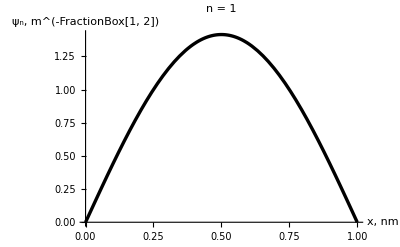

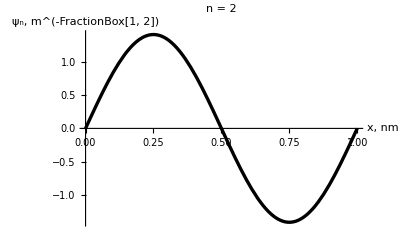

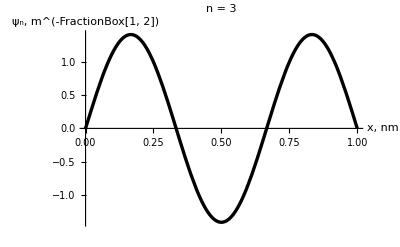

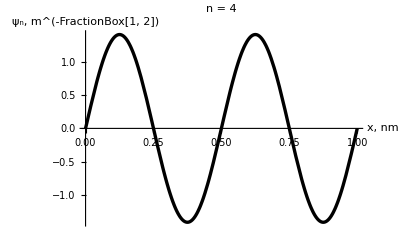

```mathematica
Do[Print[Plot[ψ2[x],{x,0,l},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm[StringForm["   n = ``  ",n],
FontFamily->"Times",FontSlant->"Italic",FontSize->12,FontWeight->"Bold"],
PlotStyle->{Black,Thickness[0.006]},
AxesLabel->{"x, nm"," ψ_n,  m^(-FractionBox[1, 2])"}]],{n,4}]
```

### Sporządzenie wykresów kwadratów unormowanych funkcji falowych na przedziale x = 0 ÷ l, dla "n" zmieniającego się od 1 do 4.

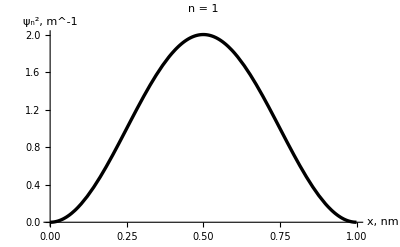

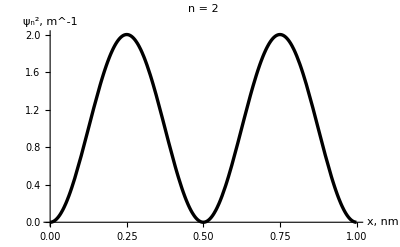

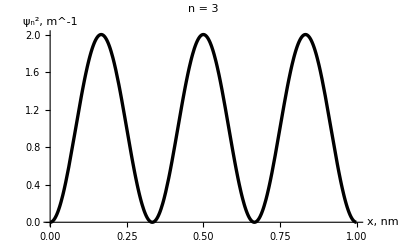

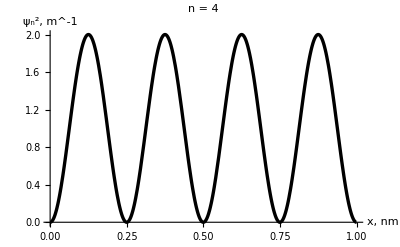

```mathematica
Do[Print[Plot[ψ2[x]^2,{x,0,l},
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm[StringForm["   n = ``  ",n],
FontFamily->"Times",FontSlant->"Italic",FontSize->12,FontWeight->"Bold"],
PlotStyle->{Black,Thickness[0.006]},
AxesLabel->{"x, nm"," ψ_n^2,  m^-1"}]],{n,4}]
```